```mathematica
projectDirectory=SetDirectory["/Users/leticiamadureira/Projects/BasisSets.jl/test/data/hydrogen"]
```

/Users/leticiamadureira/Projects/BasisSets.jl/test/data/hydrogen

```mathematica
Molecule["fluor hydride"]
```

Molecule[fluor hydride]

```mathematica
mols=Map[Molecule,{"Hydrogen","Nitrogen","Oxygen","Fluorine","Carbon Monoxide","Hydrogen Fluoride","Hydrogen Chloride","Chlorine","Lithium Hydride"}]
```

{Molecule[…],Molecule[…],Molecule[…],Molecule[…],Molecule[…],Molecule[…],Molecule[…],Molecule[…],Molecule[…]}

```mathematica
molNs={"H2","N2","O2","F2","CO","HF","HCl","Cl2","LiH"}
```

{H2,N2,O2,F2,CO,HF,HCl,Cl2,LiH}

```mathematica
molGs={"H_2","N_2","O_2","F_2","CO","HF","HCl","Cl_2","LiH"}
```

{H_2,N_2,O_2,F_2,CO,HF,HCl,Cl_2,LiH}

```mathematica
?runHF
```

```mathematica
MapThread[runHFopt[#1,#2,1,0,"sto-3g"]&,{molNs,mols}]
```

```mathematica
ress={{"H2-hf-sto-3g.log","H2-hf-sto-3g.fchk",Molecule[…]},{"N2-hf-sto-3g.log","N2-hf-sto-3g.fchk",Molecule[…]},{"O2-hf-sto-3g.log","O2-hf-sto-3g.fchk",Molecule[…]},{"F2-hf-sto-3g.log","F2-hf-sto-3g.fchk",Molecule[…]},{"CO-hf-sto-3g.log","CO-hf-sto-3g.fchk",Molecule[…]},{"HF-hf-sto-3g.log","HF-hf-sto-3g.fchk",Molecule[…]},{"HCl-hf-sto-3g.log","HCl-hf-sto-3g.fchk",Molecule[…]},{"Cl2-hf-sto-3g.log","Cl2-hf-sto-3g.fchk",Molecule[…]},{"LiH-hf-sto-3g.log","LiH-hf-sto-3g.fchk",Molecule[…]}}
```

{{H2-hf-sto-3g.log,H2-hf-sto-3g.fchk,Molecule[…]},{N2-hf-sto-3g.log,N2-hf-sto-3g.fchk,Molecule[…]},{O2-hf-sto-3g.log,O2-hf-sto-3g.fchk,Molecule[…]},{F2-hf-sto-3g.log,F2-hf-sto-3g.fchk,Molecule[…]},{CO-hf-sto-3g.log,CO-hf-sto-3g.fchk,Molecule[…]},{HF-hf-sto-3g.log,HF-hf-sto-3g.fchk,Molecule[…]},{HCl-hf-sto-3g.log,HCl-hf-sto-3g.fchk,Molecule[…]},{Cl2-hf-sto-3g.log,Cl2-hf-sto-3g.fchk,Molecule[…]},{LiH-hf-sto-3g.log,LiH-hf-sto-3g.fchk,Molecule[…]}}

```mathematica
FileNames["*.log"]
```

{Cl2-hf-sto-3g.log,CO-hf-sto-3g.log,F2-hf-sto-3g.log,H2-hf-sto-3g.log,HCl-hf-sto-3g.log,HF-hf-sto-3g.log,LiH-hf-sto-3g.log,N2-hf-sto-3g.log,O2-hf-sto-3g.log}

```mathematica
Rando
```

```mathematica
enn=Map[finalEn,ress[[All,1]]]
```

{-1.11749,-107.307,-147.538,-195.946,-111.111,-98.5717,-455.133,-909.114,-7.75103}

```mathematica
molGs
```

{H_2,N_2,O_2,F_2,CO,HF,HCl,Cl_2,LiH}

```mathematica
ennM={0.005,0.0041,0.008,-0.003,0.0082,0.001,-0.005,0.006,0.001}
```

{0.005,0.0041,0.008,-0.003,0.0082,0.001,-0.005,0.006,0.001}

```mathematica
((enn+ennM)-(enn))hartTokcal
```

```mathematica
residuals={3.137544999999933,2.5727868999962333,5.020072000006135,-1.882526999991154,5.145573800001384,0.6275090000029963,-3.1375449999971465,3.765053999982308,0.6275090000002096}
```

{3.13754,2.57279,5.02007,-1.88253,5.14557,0.627509,-3.13754,3.76505,0.627509}

```mathematica
?RandomSample
```

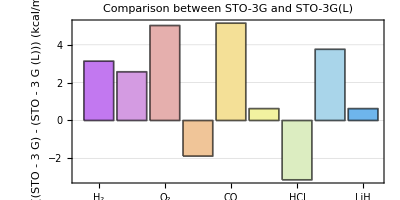

```mathematica
BarChart[residuals,Frame->True,GridLines->Automatic,AspectRatio->0.5,ChartLabels->{Map[Style[#,FontFamily->"Helvetica",FontSize->12,Black]&,molGs]},FrameStyle->Directive[Black,Thickness[0.004]],BaseStyle->FontSize->12,GridLinesStyle->Directive[Gray, Dashed,Thickness[0.0025]],FrameLabel->{None, Style["ΔE_((STO - 3  G) - (STO - 3  G (L))) (kcal/mol)",Black]},ChartStyle->{{EdgeForm[{Directive[Black,Thickness[0.0032]]}]},"Pastel"},PlotLabel->Style["Comparison between STO-3G and STO-3G(L)",Black,FontFamily->"Helvetica",Bold]]
```